# 有限温度

```mathematica
g=0.2573
```

0.2573

```mathematica
w[r_]:=2.94 Sin[1.24 Sin[0.47 r+1.94]-9.55]+3.53
```

```mathematica
T[rh_,μ_]:=1/(π rh)(1-1/2 μ^2 rh^2)
```

```mathematica
f[r_,rh_,μ_]:=1-(1/rh^4+μ^2/rh^4)r^4+ μ^4/rh^4 r^6
```

```mathematica
LT[r0_,rh_,μ_]:=2*0.1973NIntegrate[√((w[r0]^2/r0^4 *f[r0,rh,μ]^2)/(w[r]^2/r^4*f[r,rh,μ]^2*f[r0,rh,μ]-w[r0]^2/r0^4*f[r0,rh,μ]^2*f[r,rh,μ])),{r,0,r0}]
```

```mathematica
ET[r0_,rh_,μ_]:=2g NIntegrate[w[r]/r^2 √(1+f[r,rh,μ](w[r0]^2/r0^4 *f[r0,rh,μ]^2)/(w[r]^2/r^4*f[r,rh,μ]^2*f[r0,rh,μ]-w[r0]^2/r0^4*f[r0,rh,μ]^2*f[r,rh,μ]))-w[0]/r^2-w'[0]/r,{r,0,r0}]-2 g/r0*w[0]+2*g*w'[0]Log[r0]
```

```mathematica
T[2.714,0.2]//N
```

0.100007

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

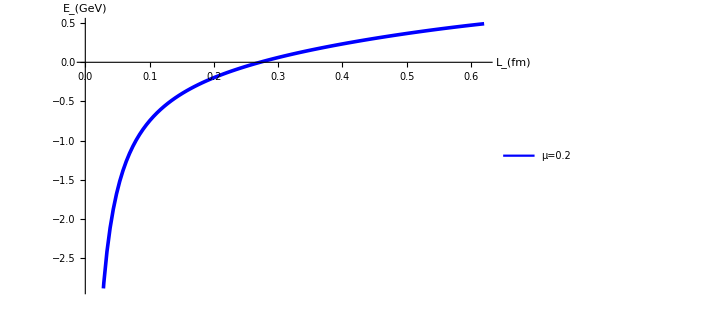

```mathematica
figEL0=ListLinePlot[ParallelTable[{Re[LT[r0,2.714,0.2]],Re[ET[r0,2.714,0.2]]},{r0,0,1.9,0.02}],
AxesLabel->{Style["L_(fm)",20,Black],Style["E_(GeV)",20,Black]},AxesStyle->Directive[Black,20],BaseStyle->{Thick},PlotStyle->{Directive[Solid,Blue,Thick,Thickness[0.005]]},PlotLegends->Placed[LineLegend[{Directive[Solid,Blue,Thick]},{"μ=0.2"},LegendMarkerSize->30],{0.85,0.4}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

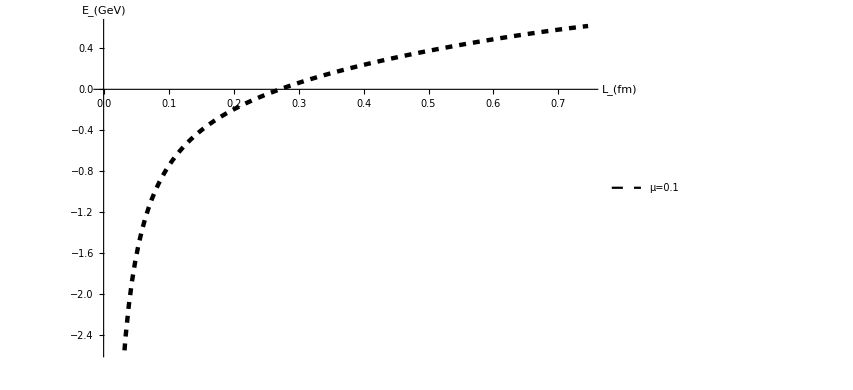

```mathematica
figEL1=ListLinePlot[ParallelTable[{Re[LT[r0,3.035,0.1]],Re[ET[r0,3.035,0.1]]},{r0,0,2.3,0.02}],AxesLabel->{Style["\!\(\*SubscriptBox[\(L\), \(\\\ \)]\)(fm)",20,Black],Style["\!\(\*SubscriptBox[\(E\), \(\\\ \)]\)(GeV)",20,Black]},AxesStyle->Directive[Black,20],BaseStyle->{Thick},PlotStyle->{Directive[Dashed,Black,Thick,Thickness[0.005]]},PlotLegends->Placed[LineLegend[{Directive[Dashed,Black,Thick]},{"μ=0.1"},LegendMarkerSize->30],{0.85,0.4}]]
```

```mathematica
|
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

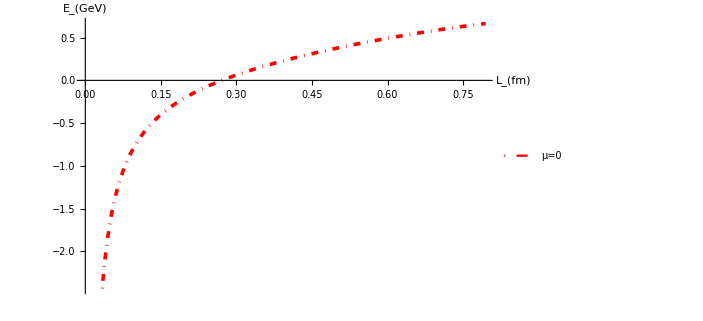

```mathematica
figEL2=ListLinePlot[ParallelTable[{Re[LT[r0,3.18,0]],Re[ET[r0,3.18,0]]},{r0,0,2.55,0.02}],
AxesLabel->{Style["L_(fm)",20,Black],Style["E_(GeV)",20,Black]},AxesStyle->Directive[Black,20],BaseStyle->{Thick},PlotStyle->{Directive[DotDashed,Red,Thick,Thickness[0.005]]},PlotLegends->Placed[LineLegend[{Directive[DotDashed,Red,,Thick]},{"μ=0"},LegendMarkerSize->30],{0.85,0.4}]]
```

```mathematica
Show[figEL2,figEL1,figEL0]
```

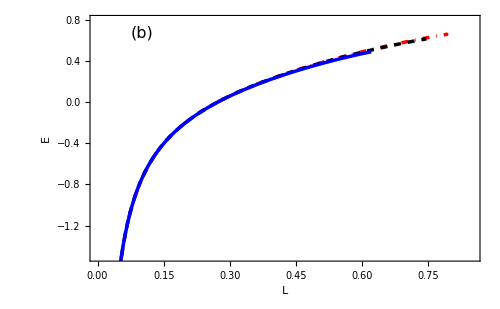

```mathematica
Show[{figEL2,figEL1,figEL0},Frame->True,FrameStyle->Directive[Black,Thin,FontFamily->"Times New Roman"],FrameLabel->{DisplayForm[RowBox[{"L"}]],DisplayForm[RowBox[{"E"}]]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],AxesOrigin->{0,-1.5},(*设置 X 轴原点在 Y=-2 处*)PlotRange->{{0,0.85},{-1.5,0.8}},(*设置 Y 轴的范围*)Epilog->{Text[Style["(b)",FontSize->16,FontFamily->"Times New Roman"],{0.1,0.6},{Center,Bottom}]},ImageSize->{500,300} (*设置图形大小为500x300*)]
```